## A hull function

```mathematica
func[x_,z_]:=a x^2+-H+α z^2
```

## Closing the Loop

```mathematica
L=375;W=164;H=30;
```

```mathematica
ClearAll[L,W,H]
```

```mathematica
b[z]:=-H+αy^2
```

```mathematica
Solve[b[0]==W,α]
```

Solve::units: Solve was unable to determine the units of quantities that appear in the input.

Solve[b[0]==164 in,α]

```mathematica
limits:=-H+H(16/L^4 x^4)<z≤ 0
```

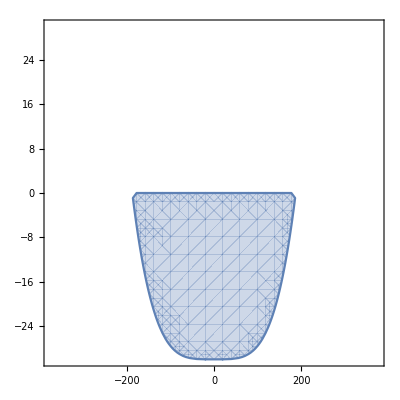

```mathematica
RegionPlot[limits,{x,-L,L},{z,-H,H}]
```

```mathematica
y:=(4 W x^2)/(2 L^2)-1/2 W √((H+z)/H)
```

```mathematica
Plot3D[y, {x,z}∈ImplicitRegion[limits, {x,z}],AxesLabel->Automatic,BoxRatios -> {L,H,W/2}]
```

-Graphics3D-

```mathematica
Integrate[y,{x,z}∈ImplicitRegion[limits, {x,z}]]
```

-2460000/7

```mathematica
Quantity[Abs[N[Integrate[y,{x,z}∈ImplicitRegion[limits, {x,z}]]]],"in^3"]
```

351429. in^3

```mathematica
UnitConvert[Quantity[351428.5714285714,("Inches")^3],"ft^3"]
```

203.373 ft^3